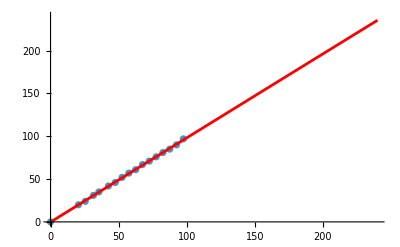

-0.19292354634084388 + 0.9854734061269065*(abs_dist) - 0.000013340676293767154*(abs_dist)**2

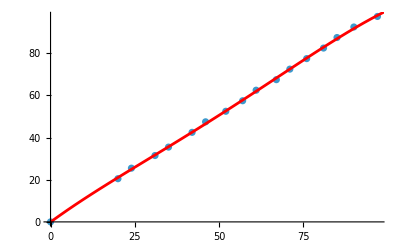

-0.06852174845793714 + 1.1692763980069285*(ball_dist) - 0.008103210588421677*(ball_dist)**2 + 0.0001347784755579611*(ball_dist)**3 - 7.016422352249597e-7*(ball_dist)**4

```mathematica
(*Input format is {dist to edge of bot, pixel distance}*)
data={{-7.5,0},{13,20},{18,24},{24,31},{28,35},{35,42},{40,46},{45,52},{50,57},{55,61},{60,67},{65,71},{70,76},{75,81},{80,85},{85,90},{90,97}};
data[[All,1]]+=7.5; 
n=2; (*what order polynomial to fit*)
bestFit=Fit[data,Table[x^k,{k,0,n}],x];
Show[ListPlot[data,PlotRange->{{0,240},{0,240}}],Plot[{bestFit},{x,0,240},PlotStyle->Red]]
pythonStr=ToString[bestFit/.{x->abs_dist},InputForm];
pythonStr=StringReplace[pythonStr,"*^"->"e"];
pythonStr=StringReplace[pythonStr,"^"->"**"];
pythonStr
data=Reverse/@data;

n=4;
bestFit=Fit[data,Table[x^k,{k,0,n}],x];
Show[ListPlot[data,PlotRange->All],Plot[{bestFit},{x,0,120},PlotStyle->Red]]
pythonStr=ToString[bestFit/.{x->ball_dist},InputForm];
pythonStr=StringReplace[pythonStr,"*^"->"e"];
pythonStr=StringReplace[pythonStr,"^"->"**"];
pythonStr
```